# exp cutoff

## fix smear and σ; calculate <g|ρ|g> for ε ϵ [5Ω,15Ω]; compare for different values of ε

## parameters

```mathematica
α=1;
Ω=1;
```

```mathematica
numSteps=10;
εMin=5Ω;εMax=15 Ω; εStepSize=Abs[εMin-εMax]/numSteps;
εValues=Table[ε,{ε,εMin,εMax,εStepSize}];
```

## smearing function

```mathematica
σ0=10^-4/Ω;
σ=σ0;
σNorm=σ/σ0;
```

```mathematica
f[x_]:=1/(σ*√π)ⅇ^(-x^2/σ^2)
ftil[k_]:=FourierTransform[f[x],x,k,FourierParameters->{1,-1},Assumptions->σ∈Reals&&σ>0]
```

## switching function

```mathematica
chiT1[t_]:=1/(r+T)1/2*(1+Cos[π/r(t+T/2)])
chiT2[t_]:=1/(r+T)
chiT3[t_]:=1/(r+T)1/2*(1+Cos[π/r(t-T/2)])
```

## k integrand

### the first interval

```mathematica
tpInt1[t_?NumericQ,k_?NumericQ]:=tpInt1[t,k]=NIntegrate[chiT1[tp]*Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,-c-r,t}]
```

```mathematica
tInt1[k_?NumericQ]:=tInt1[k]=α*NIntegrate[chiT1[t] tpInt1[t,k],
{t,-c-r,-c}]
```

### the second interval

```mathematica
tpInt2[t_,k_]:=Integrate[chiT2[tp]*Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,-c,t}]
```

```mathematica
tInt2[k_]:=α*Integrate[chiT2[t] tpInt2[t,k],
{t,-c,c}]
```

### the third interval

```mathematica
tpInt3[t_?NumericQ,k_?NumericQ]:=tpInt3[t,k]=NIntegrate[chiT3[tp]*Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,c,t}]
```

```mathematica
tInt3[k_?NumericQ]:=tInt3[k]=α*NIntegrate[chiT3[t] tpInt3[t,k],
{t,c,c+r}]
```

this integrand with the transition from Abs[k] → k taken into account (i.e. can now properly integrate from 0 to ∞ with proper factor of 2)

```mathematica
kIntegrand[k_]:=-1/π*k*ftil[k]^2*(tInt1[k]+tInt2[k]+tInt3[k])
```

## cutoff function

```mathematica
expCutoff[k_,ε_]:=ⅇ^((-Abs[k])/(2 ε));
```

## <g|ρ|g>

```mathematica
T=2;r=0.2;A=(2*c+r+(4π)/r*Sin[r^2/(4π)])^-1;
```

```mathematica
pExp=Table[α+λ^2*NIntegrate[expCutoff[k,ε]*kIntegrand[k],{k,0,∞}],{ε,εMin,εMax,εStepSize}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {255.}. NIntegrate obtained -0.185195 and 2.16604×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {255.}. NIntegrate obtained -0.188765 and 4.8191×10^-7 for the integral and error estimates.

{1-0.131835 λ^2,1-0.141189 λ^2,1-0.149166 λ^2,1-0.156105 λ^2,1-0.162236 λ^2,1-0.167721 λ^2,1-0.172679 λ^2,1-0.177201 λ^2,1-0.181355 λ^2,1-0.185195 λ^2,1-0.188765 λ^2}

## plot

```mathematica
λ=0.1;Ω=.;
```

```mathematica
dataExp=Transpose[{εValues,pExp}];
```

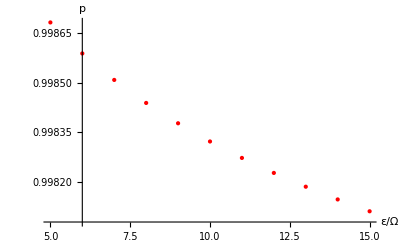

```mathematica
ListPlot[{dataExp},
AxesLabel->{ε/Ω,p},
PlotStyle->{Red},
PlotLabel->Style["",FontSize->16]]
```

## relative differences

## save the data!!

```mathematica
Export["C:/Users/Public/Documents/emma/udw-detector-shape/Cutoffs/pExpvEpsilon2.csv",dataExp];
```